```mathematica
SetDirectory[NotebookDirectory[]];
```

## 4 loop running coupling

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-(2857-5033/9 Nf+325/27 Nf^2)/128; (*for Nc=3 only*)
β3[Nf_]=-1/256((149753/6+3564 Zeta[3])-(1078361/162+6508/27 Zeta[3])Nf+(50065/162+6472/81 Zeta[3])Nf^2+1093/729 Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=1/16(202/3-20/9 Nf);(*for Nc=3 only*)
γ2[Nf_]=1/64(1249+(-2216/27-160/3 Zeta[3])Nf-140/81 Nf^2);(*for Nc=3 only*)
γ3[Nf_]=1/256(4603055/162+135680/27 Zeta[3]-8800Zeta[5]+(-91723/27-34192/9 Zeta[3]+880 Zeta[4]+18400/9 Zeta[5])Nf+(5242/243+800/9 Zeta[3]-160/3 Zeta[4])Nf^2+(-332/243+64/27 Zeta[3])Nf^3);

b0[Nf_]=-(8β0[Nf])/(2(4π)^2);
b1[Nf_]=-(32 β1[Nf])/(2(4π)^2);

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=-1/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-(β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+1/(β0[Nf]^7 t^4)( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=Quiet[NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000]];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1];
```

## Generate Spectral Functions

```mathematica
R=20000;
Mc=1.4691897661033038;
Mb=4.882;
kfinal={0.7092460807621669,-0.3437412442081188};(*100k run*)
kfinalu={1.0400912775996183,-0.44554388635406605};
kfinall={0.37840088392471555,-0.2419386020621715};
αcont={0.5129548374487685,0.002435119807500435};(*10k run*)
σcont={0.16999653850906107,0.000838106749908169};
ccont={-0.1611740456186636,0.002474788649682089};
conv=0.197327;
ReVsbVac=8/10;
```

### Define required functions

```mathematica
ImVc1[r_,mD_,α_,T_]:=T α (1-1/2 √π MeijerG[{{0},{}},{{0,1},{-1/2}},(mD^2 r^2)/4]);
ImVc[r_,mD_,α_,T_]:=T α Quiet[2NIntegrate[z/((z^2+1)^2)(1-Sinc[mD r z]),{z,0,∞}]];
```

```mathematica
ReV[r_,m_,α_,σ_,c_]:=-α m-α Exp[-m r]/r-Gamma[1/4]/(2^(3/4)√π)σ/((m^2 σ/α)^(1/4))ParabolicCylinderD[-1/2,√2(m^2 σ/α)^(1/4) r]+Gamma[1/4]/(2Gamma[3/4])σ/((m^2 σ/α)^(1/4))+c

ReVsb[r_,m_,α_,σ_,c_]:=If[ReV[r,m,α,σ,c]<ReVsbVac,ReV[r,m,α,σ,c],ReVsbVac];
```

```mathematica
ReVm0[r_,α_,σ_,c_]:=-α/r+σ r+c;
```

```mathematica
g[s_]:=Quiet[2NIntegrate[p/(p^2+1)Sinc[p s],{p,0,∞}]];
```

```mathematica
ImVs[r_,mD_,α_,σ_,T_]:=-α T (ParabolicCylinderD[-1/2,√2(mD^2 σ/α)^(1/4)r]Quiet[NIntegrate[Re[ParabolicCylinderD[-1/2,ⅈ √2 s]] s^2 g[s mD/((mD^2 σ/α)^(1/4))],{s,0,(mD^2 σ/α)^(1/4)r},MaxRecursion->20,WorkingPrecision->10]]+Re[ParabolicCylinderD[-1/2,ⅈ √2(mD^2 σ/α)^(1/4) r]]Quiet[NIntegrate[ParabolicCylinderD[-1/2,√2 s] s^2 g[s mD/((mD^2 σ/α)^(1/4))],{s,(mD^2 σ/α)^(1/4)r,∞},MaxRecursion->20,WorkingPrecision->10]]-ParabolicCylinderD[-1/2,0]Quiet[NIntegrate[ParabolicCylinderD[-1/2,√2 s] s^2 g[s mD/((mD^2 σ/α)^(1/4))],{s,0,∞},MaxRecursion->20,WorkingPrecision->10]]);
```

```mathematica
mDcal[μ_,T_,c_,d_]:=Re[Sqrt[Nc/3+nF/6]g4[μ T]T+1/(4π)Nc g4[μ T]^2 T Log[Sqrt[Nc/3+nF/6]/g4[μ T]]+c g4[μ T]^2 T+d g4[μ T]^3 T ];
```

```mathematica
rsbvac=r/.FindRoot[ReVm0[r,αcont[[1]],σcont[[1]],ccont[[1]]]==8/10,{r,1}]
```

6.14511

```mathematica
Tscancorig=Join[Table[i,{i,0.15,0.16,0.001}],Table[i,{i,0.162,0.3,0.003}]]
```

{0.15,0.151,0.152,0.153,0.154,0.155,0.156,0.157,0.158,0.159,0.16,0.162,0.165,0.168,0.171,0.174,0.177,0.18,0.183,0.186,0.189,0.192,0.195,0.198,0.201,0.204,0.207,0.21,0.213,0.216,0.219,0.222,0.225,0.228,0.231,0.234,0.237,0.24,0.243,0.246,0.249,0.252,0.255,0.258,0.261,0.264,0.267,0.27,0.273,0.276,0.279,0.282,0.285,0.288,0.291,0.294,0.297,0.3}

```mathematica
Tscanborig=Table[i,{i,0.15,0.6,0.005}]
```

{0.15,0.155,0.16,0.165,0.17,0.175,0.18,0.185,0.19,0.195,0.2,0.205,0.21,0.215,0.22,0.225,0.23,0.235,0.24,0.245,0.25,0.255,0.26,0.265,0.27,0.275,0.28,0.285,0.29,0.295,0.3,0.305,0.31,0.315,0.32,0.325,0.33,0.335,0.34,0.345,0.35,0.355,0.36,0.365,0.37,0.375,0.38,0.385,0.39,0.395,0.4,0.405,0.41,0.415,0.42,0.425,0.43,0.435,0.44,0.445,0.45,0.455,0.46,0.465,0.47,0.475,0.48,0.485,0.49,0.495,0.5,0.505,0.51,0.515,0.52,0.525,0.53,0.535,0.54,0.545,0.55,0.555,0.56,0.565,0.57,0.575,0.58,0.585,0.59,0.595,0.6}

```mathematica
eps=1/1000;ϕtab=Quiet[Join[Parallelize[Table[{x,Quiet[2NIntegrate[z/((z^2+1)^2)(1-Sinc[x z]),{z,0,∞}]]},{x,eps/100,2,10eps}]],Parallelize[Table[{x,Quiet[2NIntegrate[z/((z^2+1)^2)(1-Sinc[x z]),{z,0,∞}]]},{x,2+100eps,10,100eps}]],Parallelize[Table[{x,Quiet[2NIntegrate[z/((z^2+1)^2)(1-Sinc[x z]),{z,0,∞}]]},{x,10+1000eps,100,10000eps}]],Parallelize[Table[{x,Quiet[2NIntegrate[z/((z^2+1)^2)(1-Sinc[x z]),{z,0,∞}]]},{x,100+100000eps,10000,100000eps}]],Parallelize[Table[{x,Quiet[2NIntegrate[z/((z^2+1)^2)(1-Sinc[x z]),{z,0,∞}]]},{x,10000+10000000eps,1000000,10000000eps}]]]];
ϕinter=Interpolation[ϕtab];
```

```mathematica
eps=1/1000;gtab=Quiet[Join[Parallelize[Table[{x,x^2 g[x]},{x,eps/100,2,10eps}]],Parallelize[Table[{x,x^2 g[x]},{x,2+100eps,10,100eps}]],Parallelize[Table[{x,x^2 g[x]},{x,10+1000eps,100,10000eps}]],Parallelize[Table[{x,x^2 g[x]},{x,100+100000eps,10000,100000eps}]],Parallelize[Table[{x,x^2 g[x]},{x,10000+10000000eps,1000000,10000000eps}]]]];
ginter=Interpolation[gtab];
```

```mathematica
Clear[ParabolicCylinderI,ParabolicCylinderR];
ParabolicCylinderI[r_]=If[r<20,ParabolicCylinderD[-1/2,ⅈ √2 r],ⅇ^(r^2/2) (((1-ⅈ) √(1/r))/2^(3/4)+((3/16-(3 ⅈ)/16) (1/r)^(5/2))/2^(3/4)+((105/512-(105 ⅈ)/512) (1/r)^(9/2))/2^(3/4)+((3465/8192-(3465 ⅈ)/8192) (1/r)^(13/2))/2^(3/4)+((675675/524288-(675675 ⅈ)/524288) (1/r)^(17/2))/2^(3/4))];
ParabolicCylinderR[r_]=ParabolicCylinderD[-1/2,√2 r];
```

```mathematica
TableT[α1_,σ1_, mD1_]:=Module[{σ=σ1, α=α1,mD=mD1,μ,ratio,c,ImVsTab},
μ=(σ/α mD^2)^(1/4);
ratio=mD/μ;
R=20000;
c=Re[ParabolicCylinderI[eps] NIntegrate[( 1/ratio^2 ginter[ratio x])ParabolicCylinderR[x],{x,eps,R}]];
ImVsTab=Join[Parallelize[Table[{r,Quiet[(c-Re[ParabolicCylinderI[r]] NIntegrate[(1/ratio^2 ginter[ratio x])ParabolicCylinderR[x],{x,r,R}]- ParabolicCylinderR[r](NIntegrate[(1/ratio^2 ginter[ratio x])Re[ParabolicCylinderI[x]],{x,eps,r}]))]},{r,eps/100,1,10eps}]],Parallelize[Table[{r,Quiet[(c-Re[ParabolicCylinderI[r]] NIntegrate[(1/ratio^2 ginter[ratio x])ParabolicCylinderR[x],{x,r,R}]- ParabolicCylinderR[r](NIntegrate[( 1 1/ratio^2 ginter[ratio x])Re[ParabolicCylinderI[x]],{x,eps,r}]))]},{r,1+100eps,10+eps,100eps}]],Parallelize[Table[{r,Quiet[(c-Re[ParabolicCylinderI[r]] NIntegrate[(1/ratio^2 ginter[ratio x])ParabolicCylinderR[x],{x,r,R}]- ParabolicCylinderR[r](NIntegrate[(1/ratio^2 ginter[ratio x])Re[ParabolicCylinderI[x]],{x,eps,r}]))]},{r,11,100,1}]],Parallelize[Table[{r,Quiet[(c-Re[ParabolicCylinderI[r]] NIntegrate[(1/ratio^2 ginter[ratio x])ParabolicCylinderR[x],{x,r,R}]- ParabolicCylinderR[r](NIntegrate[(1/ratio^2 ginter[ratio x])Re[ParabolicCylinderI[x]],{x,eps,r}]))]},{r,200,1000,100}]],Parallelize[Table[{r,Quiet[(c-Re[ParabolicCylinderI[r]] NIntegrate[(1/ratio^2 ginter[ratio x])ParabolicCylinderR[x],{x,r,R}]- ParabolicCylinderR[r](NIntegrate[(1/ratio^2 ginter[ratio x])Re[ParabolicCylinderI[x]],{x,eps,r}]))]},{r,2000,20000,1000}]]];
Return[Interpolation[ImVsTab,InterpolationOrder->1]];
];
```

### Plot potentials

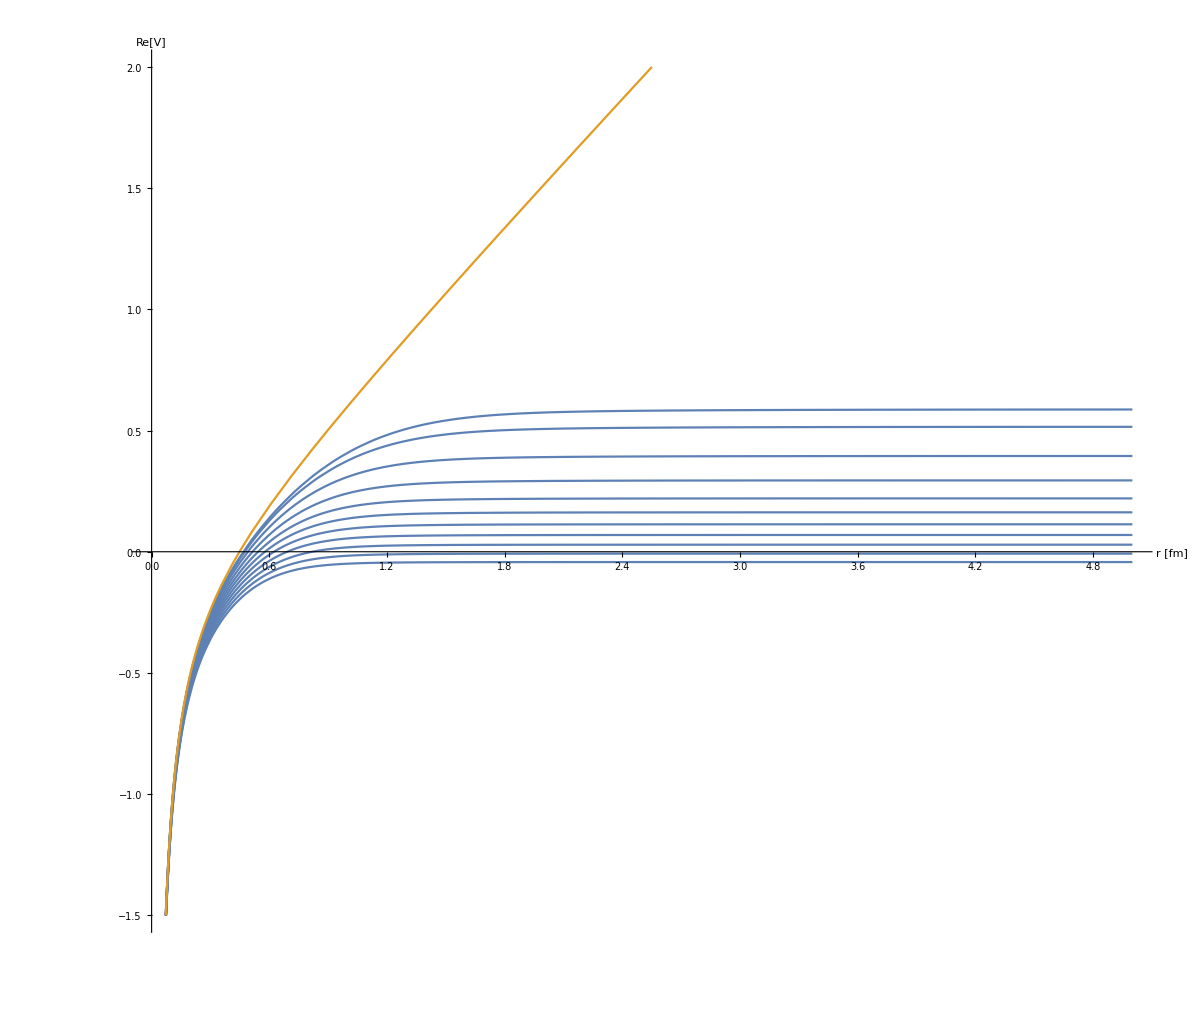

```mathematica
ReVplot=Table[ReV[r/0.197,mDcal[2π,Tscancorig[[5 l]],kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{l,Length[Tscancorig]/5}];
Plot[{ReVplot,ReVm0[r/0.197,αcont[[1]],σcont[[1]],ccont[[1]]]},{r,0,5},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{1200,1200},PlotRange->{-1.5,2},GridLines->{{conv rsbvac},{ReVsbVac}},GridLinesStyle->Directive[Gray, Dashed],BaseStyle->{FontSize->14}]
```

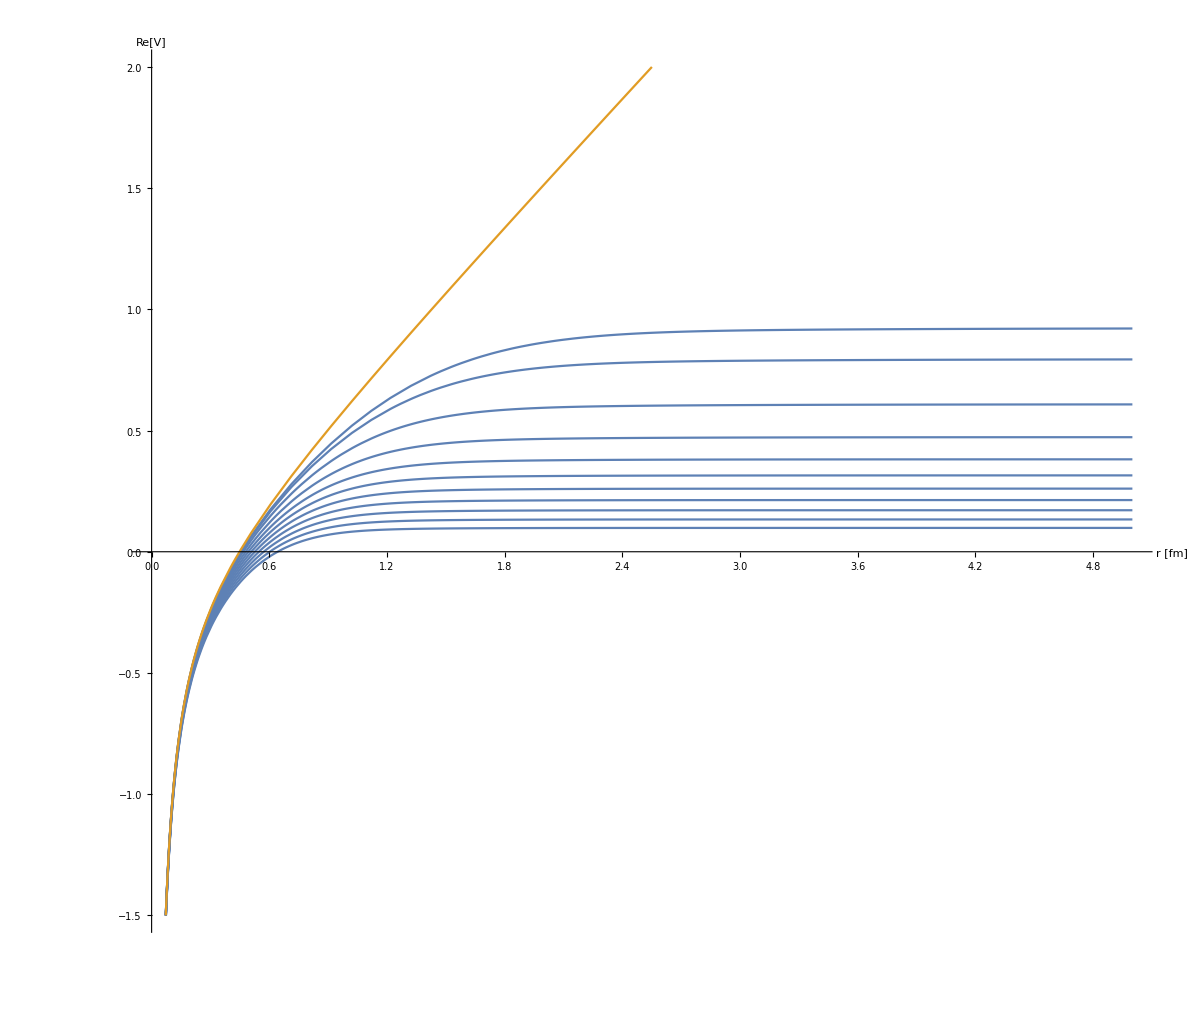

```mathematica
ReVplotl=Table[ReV[r/0.197,mDcal[2π,Tscancorig[[5 l]],kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{l,Length[Tscancorig]/5}];
Plot[{ReVplotl,ReVm0[r/0.197,αcont[[1]],σcont[[1]],ccont[[1]]]},{r,0,5},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{1200,1200},PlotRange->{-1.5,2},GridLines->{{conv rsbvac},{ReVsbVac}},GridLinesStyle->Directive[Gray, Dashed],BaseStyle->{FontSize->14}]
```

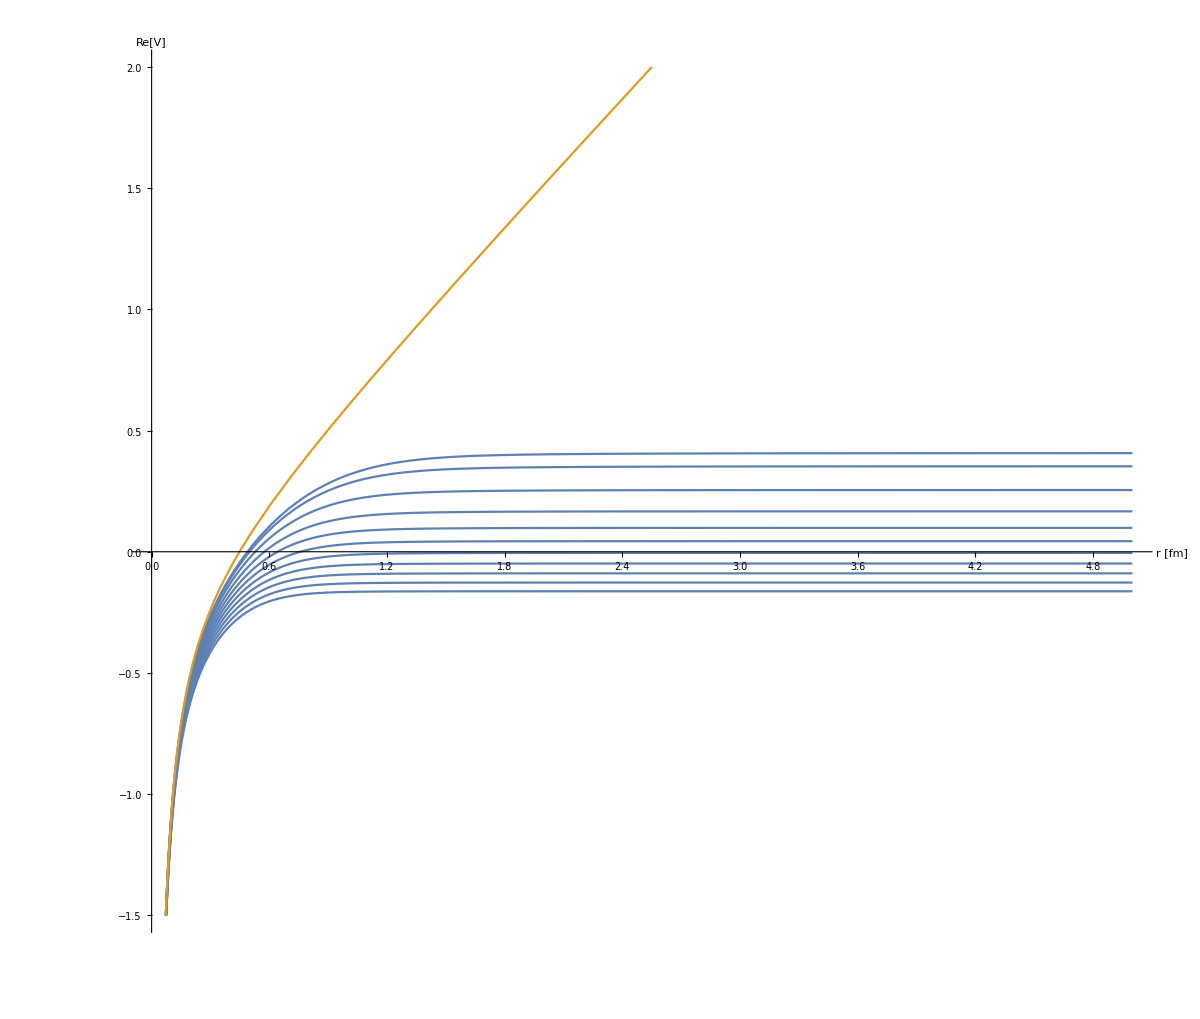

```mathematica
ReVplotu=Table[ReV[r/0.197,mDcal[2π,Tscancorig[[5 l]],kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{l,Length[Tscancorig]/5}];
Plot[{ReVplotu,ReVm0[r/0.197,αcont[[1]],σcont[[1]],ccont[[1]]]},{r,0,5},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","Re[V]"},ImageSize->{1200,1200},PlotRange->{-1.5,2},GridLines->{{conv rsbvac},{ReVsbVac}},GridLinesStyle->Directive[Gray, Dashed],BaseStyle->{FontSize->14}]
```

### Modules

```mathematica
ParallelSow[expr_]:=Sow[expr];
SetSharedFunction[ParallelSow];
```

```mathematica
δ=1/100; 
dω=0.0002;
```

#### Charmonium s - wave

```mathematica
swaveccspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinal[[1]],kfinal[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ωmin=-1,ωmax=2,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imv,V,ccsT,imvs},

imvs=TableT[α,σ,mD];

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,1/1000,10,1/100}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,101/10,25,1/10}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,26,1500,1}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccsT=ParallelTable[{ρtable[[i,1]],ρtable[[i,2]]/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["cc/swccT"<>ToString[Round[T*1000]]<>"spectra.dat",Sort[ccsT]];
];
```

```mathematica
swavecclspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinall[[1]],kfinall[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ωmin=-1,ωmax=2,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imv,V,ccsT,imvs},

imvs=TableT[α,σ,mD];

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,1/1000,10,1/100}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,101/10,25,1/10}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,26,1500,1}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];
ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccsT=ParallelTable[{ρtable[[i,1]],ρtable[[i,2]]/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["cc/swccT"<>ToString[Round[T*1000]]<>"lspectra.dat",Sort[ccsT]];
];
```

```mathematica
swaveccuspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinalu[[1]],kfinalu[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ωmin=-1,ωmax=2,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imv,V,ccsT,imvs},

imvs=TableT[α,σ,mD];

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,1/1000,10,1/100}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,101/10,25,1/10}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,26,1500,1}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccsT=ParallelTable[{ρtable[[i,1]],ρtable[[i,2]]/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["cc/swccT"<>ToString[Round[T*1000]]<>"uspectra.dat",Sort[ccsT]];
];
```

#### Charmonium p - wave

```mathematica
pwaveccspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinal[[1]],kfinal[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=1,ωmin=-1,ωmax=2,ccsT,Tstring,inf,rev,imvc,V,ρtable,ω,s0,gr,gr1,s01,gr0,s1,rhow,imvs,imv},

imvs=TableT[α,σ,mD];

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,1/1000,10,1/100}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,101/10,25,1/10}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,26,1500,1}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==(Nc M^2 α^3)/(8π)Im[1/(gr0[x])^2+36/(gr1[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccsT=ParallelTable[{ρtable[[i,1]],ρtable[[i,2]]/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Tstring=Round[T*1000];
Export["cc/pwccT"<>ToString[Tstring]<>"spectra.dat",Sort[ccsT]];
];
```

```mathematica
pwaveccuspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinalu[[1]],kfinalu[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=1,ωmin=-1,ωmax=2,ccsT,Tstring,inf,rev,imvc,V,ρtable,ω,s0,gr,gr1,s01,gr0,s1,rhow,imvs,imv},

imvs=TableT[α,σ,mD];

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,1/1000,10,1/100}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,101/10,25,1/10}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,26,1500,1}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==(Nc M^2 α^3)/(8π)Im[1/(gr0[x])^2+36/(gr1[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccsT=ParallelTable[{ρtable[[i,1]],ρtable[[i,2]]/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Tstring=Round[T*1000];
Export["cc/pwccT"<>ToString[Tstring]<>"uspectra.dat",Sort[ccsT]];
];
```

```mathematica
pwavecclspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinall[[1]],kfinall[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mc,l=1,ωmin=-1,ωmax=2,ccsT,Tstring,inf,rev,imvc,V,ρtable,ω,s0,gr,gr1,s01,gr0,s1,rhow,imvs,imv},

imvs=TableT[α,σ,mD];

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,1/1000,10,1/100}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,101/10,25,1/10}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,26,1500,1}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==(Nc M^2 α^3)/(8π)Im[1/(gr0[x])^2+36/(gr1[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccsT=ParallelTable[{ρtable[[i,1]],ρtable[[i,2]]/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Tstring=Round[T*1000];
Export["cc/pwccT"<>ToString[Tstring]<>"lspectra.dat",Sort[ccsT]];
];
```

#### Bottomonium s - wave

```mathematica
swavebbspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinal[[1]],kfinal[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mb,l=0,ωmin=-1,ωmax=3,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imv,V,bbsT,imvs},

imvs=TableT[α,σ,mD];

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,1/1000,10,1/100}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,101/10,25,1/10}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,26,1500,1}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

bbsT=ParallelTable[{ρtable[[i,1]],ρtable[[i,2]]/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["bb/swbbT"<>ToString[Round[T*1000]]<>"spectra.dat",Sort[bbsT]];
];
```

```mathematica
swavebblspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinall[[1]],kfinall[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mb,l=0,ωmin=-1,ωmax=3,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imv,V,bbsT},

TableT[α,σ,mD];

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,α T (ϕinter[mD r]+ImVsInter[(σ/α mD^2)^(1/4)r])},{r,1/1000,10,1/100}],ParallelTable[{r,α T (ϕinter[mD r]+ImVsInter[(σ/α mD^2)^(1/4)r])},{r,101/10,25,1/10}],ParallelTable[{r,α T (ϕinter[mD r]+ImVsInter[(σ/α mD^2)^(1/4)r])},{r,26,1500,1}],ParallelTable[{r,α T (ϕinter[mD r]+ImVsInter[(σ/α mD^2)^(1/4)r])},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

bbsT=ParallelTable[{ρtable[[i,1]],ρtable[[i,2]]/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["bb/swbbT"<>ToString[Round[T*1000]]<>"lspectra.dat",Sort[bbsT]];
];
```

```mathematica
swavebbuspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinalu[[1]],kfinalu[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mb,l=0,ωmin=-1,ωmax=3,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imv,V,bbsT},

TableT[α,σ,mD];

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,α T (ϕinter[mD r]+ImVsInter[(σ/α mD^2)^(1/4)r])},{r,1/1000,10,1/100}],ParallelTable[{r,α T (ϕinter[mD r]+ImVsInter[(σ/α mD^2)^(1/4)r])},{r,101/10,25,1/10}],ParallelTable[{r,α T (ϕinter[mD r]+ImVsInter[(σ/α mD^2)^(1/4)r])},{r,26,1500,1}],ParallelTable[{r,α T (ϕinter[mD r]+ImVsInter[(σ/α mD^2)^(1/4)r])},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

bbsT=ParallelTable[{ρtable[[i,1]],ρtable[[i,2]]/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["bb/swbbT"<>ToString[Round[T*1000]]<>"uspectra.dat",Sort[bbsT]];
];
```

#### Bottomonium p - wave

```mathematica
pwavebbspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinal[[1]],kfinal[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mb,l=1,ωmin=-1,ωmax=3,ccsT,Tstring,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imv,V,bbsT,imvs},

imvs=TableT[α,σ,mD];

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,1/1000,10,1/100}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,101/10,25,1/10}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,26,1500,1}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==(Nc M^2 α^3)/(8π)Im[1/(gr0[x])^2+36/(gr1[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

bbsT=ParallelTable[{ρtable[[i,1]],ρtable[[i,2]]/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Tstring=Round[T*1000];
Export["bb/pwbbT"<>ToString[Tstring]<>"spectra.dat",Sort[bbsT]];
];
```

```mathematica
pwavebblspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinall[[1]],kfinall[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mb,l=1,ωmin=-1,ωmax=3,ccsT,Tstring,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imvs,imv,V,bbsT},

imvs=TableT[α,σ,mD];

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,1/1000,10,1/100}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,101/10,25,1/10}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,26,1500,1}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==(Nc M^2 α^3)/(8π)Im[1/(gr0[x])^2+36/(gr1[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

bbsT=ParallelTable[{ρtable[[i,1]],ρtable[[i,2]]/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Tstring=Round[T*1000];
Export["bb/pwbbT"<>ToString[Tstring]<>"lspectra.dat",Sort[bbsT]];
];
```

```mathematica
pwavebbuspectra[n_,Tscan_]:=Block[{T=Tscan[[n]],mD=mDcal[2π,Tscan[[n]],kfinalu[[1]],kfinalu[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=Mb,l=1,ωmin=-1,ωmax=3,ccsT,Tstring,inf,ρtable,ω,rhow,gr0,s1,s01,rev,imvs,imv,V,bbsT},

imvs=TableT[α,σ,mD];

rev=Interpolation[Join[ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1/1000,10,1/100}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,101/10,25,1/10}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,26,1500,1}],ParallelTable[{r,ReVsb[r,mD,α,σ,c]},{r,1510,20000,1000}]]];
imv=Interpolation[Join[ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,1/1000,10,1/100}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,101/10,25,1/10}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,26,1500,1}],ParallelTable[{r,α T (ϕinter[mD r]+imvs[(σ/α mD^2)^(1/4)r])},{r,1510,20000,1000}]]];
V[x_]:=rev[x]+ⅈ imv[x];

ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==(Nc M^2 α^3)/(8π)Im[1/(gr0[x])^2+36/(gr1[x])^2],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

bbsT=ParallelTable[{ρtable[[i,1]],ρtable[[i,2]]/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Tstring=Round[T*1000];
Export["bb/pwbbT"<>ToString[Tstring]<>"uspectra.dat",Sort[bbsT]];
];
```

#### Run modules

```mathematica
Off[NIntegrate::inumr]
```

```mathematica
Do[swaveccspectra[i,Tscancorig],{i,Length[Tscancorig]}]//AbsoluteTiming
```

```mathematica
Do[swavecclspectra[i,Tscancorig],{i,Length[Tscancorig]}]//AbsoluteTiming
```

```mathematica
Do[swaveccuspectra[i,Tscancorig],{i,Length[Tscancorig]}]//AbsoluteTiming
```

```mathematica
Tscanpwave=Table[x,{x,0.15,0.19,0.001}]
```

{0.15,0.151,0.152,0.153,0.154,0.155,0.156,0.157,0.158,0.159,0.16,0.161,0.162,0.163,0.164,0.165,0.166,0.167,0.168,0.169,0.17,0.171,0.172,0.173,0.174,0.175,0.176,0.177,0.178,0.179,0.18,0.181,0.182,0.183,0.184,0.185,0.186,0.187,0.188,0.189,0.19}

```mathematica
Tscanpwave[[8;;]]
```

{0.157,0.158,0.159,0.16,0.161,0.162,0.163,0.164,0.165,0.166,0.167,0.168,0.169,0.17,0.171,0.172,0.173,0.174,0.175,0.176,0.177,0.178,0.179,0.18,0.181,0.182,0.183,0.184,0.185,0.186,0.187,0.188,0.189,0.19}

```mathematica
Do[pwaveccspectra[i,Tscanpwave[[8;;]]],{i,Length[Tscanpwave[[8;;]]]}]//AbsoluteTiming
```

```mathematica
Do[pwaveccuspectra[i,Tscanpwave[[8;;]]],{i,Length[Tscanpwave[[8;;]]]}]//AbsoluteTiming
```

```mathematica
Do[pwavecclspectra[i,Tscanpwave],{i,Length[Tscanpwave]}]//AbsoluteTiming
```

```mathematica
Tscanborig[[36;;44]]
```

{0.325,0.33,0.335,0.34,0.345,0.35,0.355,0.36,0.365}

```mathematica
Do[swavebbspectra[i,Tscanborig[[36;;44]]],{i,Length[Tscanborig[[36;;44]]]}]//AbsoluteTiming
```

{1094.6,Null}

```mathematica
Do[swavebbuspectra[i,Tscanborig],{i,Length[Tscanborig]}]//AbsoluteTiming
```

```mathematica
Do[swavebblspectra[i,Tscanborig],{i,Length[Tscanborig]}]//AbsoluteTiming
```

```mathematica
Do[pwavebbspectra[i,Tscancorig],{i,Length[Tscancorig]}]//AbsoluteTiming
```

{13393.2,Null}

```mathematica
Do[pwavebbuspectra[i,Tscancorig],{i,Length[Tscancorig]}]//AbsoluteTiming
```

{14751.4,Null}

```mathematica
Do[pwavebblspectra[i,Tscancorig],{i,Length[Tscancorig]}]//AbsoluteTiming
```

{17309.6,Null}

## Continuum Energies

```mathematica
2Mc+Table[ReVsb[100000,mDcal[2π,Tscancorig[[i]],kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tscancorig]}]
```

{3.59975,3.57936,3.5603,3.54242,3.5256,3.50972,3.49469,3.48043,3.46686,3.45393,3.44159,3.41845,3.38706,3.35894,3.33346,3.31017,3.28871,3.26879,3.25021,3.23277,3.21634,3.20078,3.18601,3.17193,3.15847,3.14582,3.13406,3.12269,3.11166,3.10097,3.09057,3.08045,3.0706,3.06098,3.0516,3.04242,3.03344,3.02465,3.01604,3.00759,2.9993,2.99115,2.98315,2.97528,2.96753,2.95991,2.9524,2.945,2.9377,2.93051,2.9234,2.91639,2.90947,2.90262,2.89586,2.88918,2.88257,2.87603}

```mathematica
2Mc+Table[ReVsb[100000,mDcal[2π,Tscancorig[[i]],kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tscancorig]}]
```

{3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73838,3.73316,3.71251,3.67487,3.62579,3.58359,3.54667,3.51391,3.48452,3.45788,3.43352,3.4111,3.39033,3.37097,3.35284,3.33579,3.31969,3.30477,3.29114,3.27807,3.26551,3.25343,3.24177,3.2305,3.21961,3.20905,3.1988,3.18884,3.17916,3.16973,3.16053,3.15156,3.1428,3.13424,3.12586,3.11766,3.10962,3.10174,3.09401,3.08641,3.07896,3.07163,3.06442,3.05733,3.05035,3.04347,3.03669,3.03002,3.02343,3.01693}

```mathematica
2Mc+Table[ReVsb[100000,mDcal[2π,Tscancorig[[i]],kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tscancorig]}]
```

{3.39844,3.38409,3.37048,3.35753,3.34518,3.33337,3.32207,3.31123,3.30081,3.29079,3.28113,3.2628,3.23746,3.21428,3.19292,3.17307,3.15453,3.13711,3.12066,3.10506,3.09022,3.07605,3.06248,3.04944,3.03689,3.02498,3.0138,3.00292,2.99233,2.98199,2.9719,2.96204,2.95239,2.94294,2.93368,2.92459,2.91567,2.9069,2.89828,2.8898,2.88145,2.87323,2.86512,2.85713,2.84924,2.84146,2.83378,2.82619,2.81869,2.81127,2.80394,2.79668,2.7895,2.78239,2.77536,2.76839,2.76148,2.75463}

```mathematica
2Mb+Table[ReVsb[100000,mDcal[2π,Tscanborig[[i]],kfinal[[1]],kfinal[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tscanborig]}]
```

{10.4254,10.3353,10.2672,10.2127,10.1673,10.1284,10.0944,10.0641,10.0367,10.0116,9.98851,9.96747,9.94831,9.93012,9.91279,9.89622,9.88032,9.86503,9.85027,9.83601,9.82219,9.80877,9.79572,9.78302,9.77062,9.75851,9.74668,9.73509,9.72373,9.71259,9.70165,9.6909,9.68032,9.66992,9.65967,9.64958,9.63962,9.6298,9.6201,9.61053,9.60107,9.59172,9.58247,9.57332,9.56427,9.5553,9.54643,9.53763,9.52892,9.52028,9.51172,9.50322,9.4948,9.48644,9.47814,9.4699,9.46172,9.4536,9.44553,9.43752,9.42955,9.42164,9.41377,9.40595,9.39818,9.39044,9.38275,9.3751,9.36749,9.35992,9.35239,9.34489,9.33743,9.33,9.32261,9.31525,9.30792,9.30062,9.29335,9.28611,9.27891,9.27172,9.26457,9.25744,9.25034,9.24326,9.23621,9.22918,9.22218,9.2152,9.20824}

```mathematica
2Mb+Table[ReVsb[100000,mDcal[2π,Tscanborig[[i]],kfinall[[1]],kfinall[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tscanborig]}]
```

{10.564,10.564,10.5381,10.4514,10.3841,10.3294,10.2835,10.244,10.2093,10.1785,10.1506,10.1258,10.1037,10.083,10.0636,10.0452,10.0278,10.0112,9.99535,9.98015,9.96555,9.95148,9.9379,9.92477,9.91204,9.89968,9.88766,9.87597,9.86456,9.85343,9.84255,9.83191,9.82149,9.81128,9.80127,9.79143,9.78177,9.77227,9.76293,9.75373,9.74467,9.73574,9.72694,9.71825,9.70968,9.70121,9.69285,9.68459,9.67642,9.66833,9.66034,9.65243,9.64459,9.63684,9.62915,9.62154,9.61399,9.60651,9.59909,9.59174,9.58444,9.5772,9.57001,9.56287,9.55579,9.54876,9.54177,9.53483,9.52794,9.52108,9.51427,9.50751,9.50078,9.49409,9.48743,9.48082,9.47424,9.46769,9.46118,9.4547,9.44825,9.44184,9.43545,9.42909,9.42277,9.41647,9.41019,9.40395,9.39773,9.39153,9.38536}

```mathematica
2Mb+Table[ReVsb[100000,mDcal[2π,Tscanborig[[i]],kfinalu[[1]],kfinalu[[2]]],αcont[[1]],σcont[[1]],ccont[[1]]],{i,1,Length[Tscanborig]}]
```

{10.2241,10.159,10.1068,10.0631,10.0255,9.99238,9.96273,9.93579,9.91105,9.8881,9.86664,9.84684,9.82854,9.81103,9.79421,9.77801,9.76237,9.74722,9.73252,9.71823,9.70432,9.69074,9.67748,9.66451,9.65181,9.63935,9.62713,9.61512,9.60331,9.5917,9.58026,9.56898,9.55786,9.54689,9.53606,9.52536,9.51479,9.50434,9.494,9.48376,9.47363,9.4636,9.45366,9.44381,9.43405,9.42437,9.41477,9.40524,9.39578,9.3864,9.37708,9.36783,9.35864,9.34951,9.34043,9.33142,9.32245,9.31354,9.30468,9.29587,9.28711,9.27839,9.26971,9.26108,9.25249,9.24395,9.23544,9.22697,9.21853,9.21013,9.20177,9.19345,9.18515,9.17689,9.16866,9.16046,9.15229,9.14415,9.13604,9.12796,9.1199,9.11188,9.10387,9.0959,9.08794,9.08002,9.07211,9.06423,9.05637,9.04854,9.04072}